```mathematica
l[n_]:=Import["pddf_alpha-curve_tot_10%_r=6_seed_"<>ToString[n]<>".dat"];
```

```mathematica
ListPlot[Table[l[i],{i,1,100}],ImageSize->600]
```

-Graphics-

```mathematica
listableinterpol=Table[Interpolation[l[i]],{i,1,100}];
```

```mathematica
Rgs=Table[(1/2 NIntegrate[r^2 listableinterpol[[i]][r],{r,0,Max[l[i]]}])^(1/2),{i,1,Length[listableinterpol]}];
Export["Rg.dat",Rgs]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {90.7112}. NIntegrate obtained 1431.57 and 0.175531 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {87.233}. NIntegrate obtained 1442.5 and 0.168717 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {102.511}. NIntegrate obtained 1434.3 and 0.177938 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Rg.dat

```mathematica
Mean[Rgs]
```

26.8365

```mathematica
StandardDeviation[Rgs]/Sqrt[Length[Rgs]]
```

0.00721214

```mathematica
(*Calculate the average of pddf*)
```

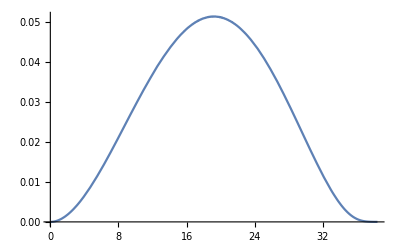

```mathematica
avgpddf[x_]:=Sum[listableinterpol⟦i⟧[x],{i,1,100}]/100;
avgplot=Plot[avgpddf[x],{x,Max[Table[Min[l[i]⟦All,1⟧],{i,1,100}]],Min[Table[Max[l[i]⟦All,1⟧],{i,1,100}]]}]
```

```mathematica
avgdata=Table[{x,avgpddf[x]},{x,Max[Table[Min[l[i]⟦All,1⟧],{i,1,100}]],Min[Table[Max[l[i]⟦All,1⟧],{i,1,100}]],.2}];
```

```mathematica
Export["mean_pddf.dat",avgdata]
```

mean_pddf_sphere_rmax=20.dat

```mathematica
ready=Table[listableinterpol⟦i⟧[j],{i,1,100},{j,Max[Table[Min[l[k]⟦All,1⟧],{k,1,100}]],Min[Table[Max[l[k]⟦All,1⟧],{k,1,100}]],.2}];
```

```mathematica
Length[avgdata]
```

424

```mathematica
SEMpddf=Table[StandardDeviation[ready⟦All,i⟧]/Sqrt[Length[ready⟦All,i⟧]],{i,1,Length[avgdata]}];
```

```mathematica
Length[SEMpddf]
```

424

```mathematica
rSEMpddf=Table[i,{i,Max[Table[Min[l[j][[All,1]]],{j,1,100}]],Min[Table[Max[l[j][[All,1]]],{j,1,100}]],.2}];
```

```mathematica
Length[rSEMpddf]
```

427

```mathematica
SEMpddfdata=Table[{rSEMpddf⟦i⟧,SEMpddf⟦i⟧},{i,1,Length[rSEMpddf]}];
Export["SEM-pddf.dat",SEMpddfdata]
```

SEM-pddf_alpha-curves_sphere_rmax=20.dat

```mathematica
(*================================================================================*)
```

```mathematica
(*Calculating SAS intensities*)
```

```mathematica
sf[n_]:=Table[{x,listableinterpol⟦n⟧[x]},{x,Max[Table[Min[l[i]⟦All,1⟧],{i,1,100}]],Min[Table[Max[l[i]⟦All,1⟧],{i,1,100}]],.2}];
sfcoordstable=Table[sf[i],{i,1,100}];
```

```mathematica
qsf=Table[i,{i,0.01,1,.002}];Pqsf[n_]:=List[#,1/2 Total[Differences[Partition[Riffle[sfcoordstable⟦n⟧⟦All,1⟧,sfcoordstable⟦n⟧[[All,2]] Sin[# sfcoordstable⟦n⟧⟦All,1⟧]/(# sfcoordstable⟦n⟧⟦All,1⟧)],2][[All,1]]] ListCorrelate[{1,1},Partition[Riffle[sfcoordstable⟦n⟧⟦All,1⟧,sfcoordstable⟦n⟧[[All,2]] Sin[# sfcoordstable⟦n⟧⟦All,1⟧]/(# sfcoordstable⟦n⟧⟦All,1⟧)],2][[All,2]]]]]&/@qsf;
plotandexport[n0_]:=Module[{n=n0},
plot=ListLogLogPlot[{Pqsf[n]},PlotStyle->{Red,Blue,Green,Black},Joined->False,PlotRange->All];
Export["SAS_alpha-curve_cylinder_r=5_seed_"<>ToString[n]<>".dat",Pqsf[n]];plot];
Table[plotandexport[i],{i,13,100}];
```

```mathematica
(*Calculating the average SAS intensity*)
```